```mathematica
Needs["FourierSeries`"]
```

```mathematica
(*Density of states for one spin-species:*)
```

```mathematica
Dens[en_]:=NFourierTransform[(BesselJ[0,t/Sqrt[6]])^3/Sqrt[2Pi],t,en]
```

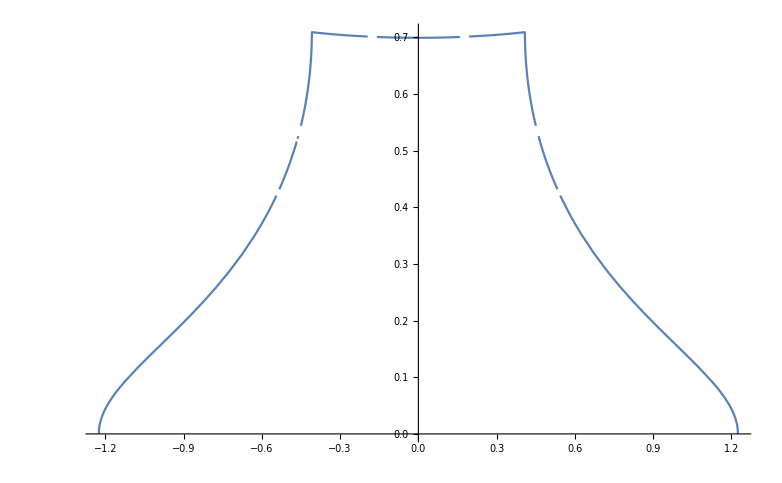

```mathematica
Plot[Dens[x],{x,-Sqrt[6]/2,Sqrt[6]/2}]
```

```mathematica
Denstab={N@#,N@Dens[#]}&/@Table[(Sqrt[6]/2)*i/1000,{i,-1000,1000}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-4.81037×10^7}. NIntegrate obtained 0.000241241  + 0.\ ⅈ and 0.00214756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.81037×10^7}. NIntegrate obtained 0.0241122  + 0.\ ⅈ and 8.56765×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.81037×10^7}. NIntegrate obtained 0.0341255  + 5.63785×10^-17\ ⅈ and 1.43846×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{{-1.22474,0.0000962414+0. ⅈ},{-1.22352,0.00961938+0. ⅈ},{-1.2223,0.0136141+2.24918×10^-17 ⅈ},{-1.22107,0.0166863+0. ⅈ},{-1.21985,0.0192822+0. ⅈ},1991,{1.21985,0.0192822+0. ⅈ},{1.22107,0.0166863+0. ⅈ},{1.2223,0.0136141-2.24918×10^-17 ⅈ},{1.22352,0.00961938+0. ⅈ},{1.22474,0.0000962414+0. ⅈ}}
 |  |  |  |

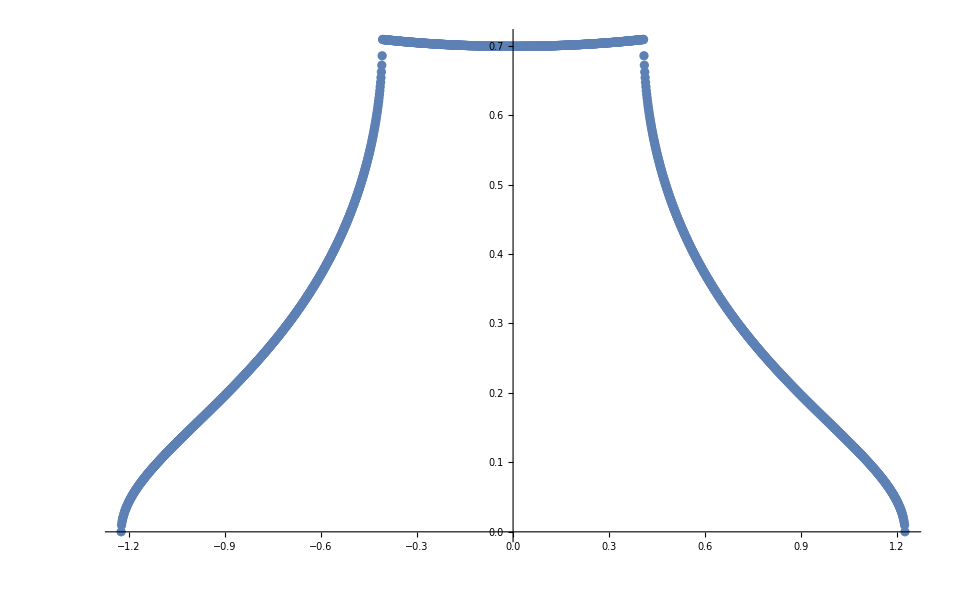

```mathematica
Show[{ListPlot[Denstab]}]
```

```mathematica
Export["dens3d.dat",Denstab]
```

dens3d.dat

```mathematica
ekin[beta_]:=-(Sqrt[1.5]/beta)*NIntegrate[(BesselJ[0,x/Sqrt[6]])^2*BesselJ[1,x/Sqrt[6]]/Sinh[Pi*x/b],{x,-Infinity,+Infinity}]
```

```mathematica
ekintab={#,ekin[#]}&/@Table[8.0+92.0*i/10000,{i,0,10000}]
```

```mathematica
Export["EkinU0.dat",ekin1tab]
```

```mathematica
f[t_]=FullSimplify@FourierTransform[1/(1+Exp[x*b]),x,t]
```

-(ⅈ √(π/2) Csch[(π t)/b])/b

```mathematica
FullSimplify@Integrate[-Sqrt[3/2]/Pi*(BesselJ[0, x])^2*BesselJ[1, x]/x, {x, -Infinity, +Infinity}]
```

-(√(3/2) MeijerG[{{1/2},{3/2,3/2}},{{0,1},{0}},1/4])/π^(3/2)

```mathematica
N@Sqrt[3/2]*MeijerG[{{1/2},{3/2,3/2}},{{0,1},{0}},1/4]/Sqrt[Pi]^3
```

0.409236

```mathematica
(*Calculate E_kin and E_pot with the Atomic Limit self-energy*)
```

```mathematica
(*Calculation only for half-filling!!! Out of half-filling->replace eps->eps-m+Un/2*)
```

```mathematica
fermi[beta_,eps_]:=1/(Exp[beta*eps]+1)
```

```mathematica
zero1[U_,eps_]:=(1/2)*(eps+Sqrt[eps^2+U^2])
```

```mathematica
zero2[U_,eps_]:=(1/2)*(eps-Sqrt[eps^2+U^2])
```

```mathematica
ekinAL[U_,beta_]:=NIntegrate[Sqrt[eps^2+U^2]^(-1)*(fermi[beta,zero1[U,eps]]*zero1[U,eps]-fermi[beta,zero2[U,eps]]*zero2[U,eps])*2.0*Dens[eps]*eps,{eps,-Sqrt[6]/2,Sqrt[6]/2}]
```

```mathematica
epotAL[U_,beta_]:=(U/4)*(1+U*NIntegrate[Sqrt[eps^2+U^2]^(-1)*(fermi[beta,zero1[U,eps]]-fermi[beta,zero2[U,eps]])*Dens[eps],{eps,-Sqrt[6]/2,Sqrt[6]/2}])
```

```mathematica
ekinALtab={#,ekinAL[4,#]}&/@Table[8.0+92.0*i/10,{i,0,0}]
```

$Aborted

```mathematica
FourierTransform[Sqrt[eps^2+4^2]^(-1)*(fermi[10,zero1[4,eps]]*zero1[4,eps]-fermi[10,zero2[4,eps]]*zero2[4,eps]),eps,t]
```

$Aborted

```mathematica
NIntegrate[Sqrt[eps^2+4^2]^(-1)*(fermi[10,zero1[4,eps]]*zero1[4,eps]-fermi[10,zero2[4,eps]]*zero2[4,eps])*Exp[I*eps*t]*BesselJ[0,t/Sqrt[6]]^3,{eps,-Sqrt[6]/2,Sqrt[6]/2},{t,-Infinity,+Infinity}]
```

$Aborted